# Asymmetric Quartic Large-order WKB

We compute the large order transseries asymptotics using Bender Wu for the 1-d Schroedinger problem  -ℏ/2ψ’’(x) +ψ(x)V(x) = E ψ(x) with V(x) = x^4-αx^3+βx^2+γx.
The classical momentum  (p(x;E))^2=2(E-V) defines an associated WKB curve given by a genus-one hyperelliptic curve Σ : y^2=2(E-V(x)) 
y^2= 2E -2 (x^4-αx^3+βx^2+γx) .

This is the toy analogue of the spin-weighted spheroidal quartic. Meynig’s spheroidal analysis uses exact WKB quantum periods and a perturbative/nonperturbative relation to build the transseries for the eigenvalue; the paper explicitly frames the spheroidal problem in terms of all-orders WKB, quantum periods, and a first exponential correction checked by numerical resurgence.

```mathematica
ClearAll["Global`*"];

Needs["BenderWu`"];
```

```mathematica
(* Borel Pade params *)
L=35;
M=35;
```

```mathematica
ClearAll[x,g,a,b,nu,order];

pars={a->1/5,b->1}; (* V params *)

V[x_]:=x^2/2+a x^3+b x^4;
```

```mathematica
(* BenderWu convention: you give the potential without manually inserting the coupling powers. For example, for the quartic oscillator, it treats the quartic as entering at order g^2 *)
```

```mathematica
BenderWu[x^2/2+x^4,x,3,2]
```

{{0,7/2,75/4,-1575/8},{{0,-3/2,0,1,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,225/16,0,0,0,-15/8,0,-1/4,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,-35775/128,0,0,0,315/16,0,135/32,0,115/192,0,1/32,0,0,0,0}},{x,3,4,1}}

## Run BW to get the WKB Energy coefficients

```mathematica
(* BW order *)
nu=0; (* BW level *)
order=80;
(* E(n;ℏ) = ∑_r Subscript[E^(0), r] ℏ^r *)
bwRaw=BenderWu[x^2/2+a x^3+b x^4,x,nu,order,Simplify->True];

coeffsSym=BWProcess[bwRaw,Output->"Energy",OutputStyle->"Array"];

coeffs=N[coeffsSym/. pars,10];
```

```mathematica
ClearAll[EnergySeries];

EnergySeries[coeffs_List,z_]:=Sum[coeffs[[k+1]] z^k,{k,0,Length[coeffs]-1}];

Epert[z_]:=EnergySeries[coeffs,z];
```

## Borel Pade

```mathematica
ClearAll[BorelCoeffs,BorelSeries];

(* --- Borel transform of E series is ℬE(t) = ∑_k Subscript[E, k] t^k/(k!) --- *)
BorelCoeffs[coeffs_List]:=Table[coeffs[[k+1]]/k!,{k,0,Length[coeffs]-1}];

BorelSeries[coeffs_List,t_]:=Sum[coeffs[[k+1]]/k! t^k,{k,0,Length[coeffs]-1}];

borelCoeffs=BorelCoeffs[coeffs];
```

```mathematica
ClearAll[BorelPade];
(* --- Borel Pade  ℬE(t) = [L/M](t)   --- *)
BorelPade[coeffs_List,t_,L_Integer,M_Integer]:=Module[{nmax,ser},nmax=Min[Length[coeffs]-1,L+M];
ser=Sum[coeffs[[k+1]]/k! t^k,{k,0,nmax}];
PadeApproximant[ser,{t,0,{L,M}}]];


BP[t_]=BorelPade[coeffs,t,L,M];
```

```mathematica
ClearAll[BorelTransformSeries,BorelPade];

BorelTransformSeries[coeffs_List,t_,nmax_:Automatic]:=Module[{n},n=If[nmax===Automatic,Length[coeffs]-1,nmax];
Sum[coeffs[[k+1]]/k! t^k,{k,0,Min[n,Length[coeffs]-1]}]];

BorelPade[coeffs_List,t_,L_Integer,M_Integer]:=Module[{nmax,ser},nmax=Min[Length[coeffs]-1,L+M];
ser=BorelTransformSeries[coeffs,t,nmax];
PadeApproximant[ser,{t,0,{L,M}}]];
```

```mathematica
ClearAll[BorelPadeSum];

(* --- Borel resummation  Subscript[𝒮, θ] E(t) = (∫_0)^((∞e)^-iθ)dt ℬ(zt) e^-t   --- *)

Options[BorelPadeSum]={WorkingPrecision->80,AccuracyGoal->20,PrecisionGoal->20,MaxRecursion->100,DirectionAngle->0};

BorelPadeSum[coeffs_List,z0_?NumericQ,L_Integer,M_Integer,OptionsPattern[]]:=Module[{t,s,theta,bpExpr,wp,ag,pg,mr,z},theta=OptionValue[DirectionAngle];
wp=OptionValue[WorkingPrecision];
ag=OptionValue[AccuracyGoal];
pg=OptionValue[PrecisionGoal];
mr=OptionValue[MaxRecursion];
z=SetPrecision[z0,wp];
bpExpr=BorelPade[coeffs,t,L,M];
NIntegrate[Evaluate[Exp[-s Exp[I theta]]*(bpExpr/. t->z s Exp[I theta])*Exp[I theta]],{s,0,Infinity},WorkingPrecision->wp,AccuracyGoal->ag,PrecisionGoal->pg,MaxRecursion->mr,Exclusions->None,Method->{"GlobalAdaptive","SymbolicProcessing"->0}]];
```

```mathematica
z0=0.05;

EBP=BorelPadeSum[coeffs,z0,4,4]
```

NIntegrate::precw: The precision of the argument function ((ⅇ^-s$489111 (0.5+«6»))/(1+0.2436169048 s$489111+«44» «1»-«44» («8»)^3-0.00002451236912 s$489111^4)) is less than WorkingPrecision (80.).

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 100 recursive bisections in s$489111 near {s$489111} = {17.823740183663222023299949714127840470871494360907414282588804652976320368852095}. NIntegrate obtained 0.5310590467442521305089359348236987349685956268772164827666062929513294208367599 and 2.0340710434147750321742223663755975569629628792991910466285531107283012413673834×10^-9 for the integral and error estimates.

0.5310590467442521305089359348236987349685956268772164827666062929513294208367599

```mathematica
eps=10^-6;

EBPplus=BorelPadeSum[res["Coefficients"],0.05,4,4,DirectionAngle->eps,WorkingPrecision->50,AccuracyGoal->20,PrecisionGoal->20];

EBPminus=BorelPadeSum[res["Coefficients"],0.05,4,4,DirectionAngle->-eps,WorkingPrecision->50,AccuracyGoal->20,PrecisionGoal->20];

{EBPplus,EBPminus,EBPplus-EBPminus}
```

NIntegrate::precw: The precision of the argument function ((ⅇ^(ⅈ/1000000-s$485444) (0.5+(«83»+«80» ⅈ) s$485444+(«98»+«1») «1»-(«98»+«92» ⅈ) («8»)^3-(«97»+«93» ⅈ) s$485444^4))/(1+«6»)) is less than WorkingPrecision (50.).

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::precw: The precision of the argument function ((ⅇ^(-ⅈ/1000000-s$485473) (0.5+(«83»-«80» ⅈ) s$485473+(«98»-«1») «1»-(«98»-«92» ⅈ) («8»)^3-(«97»-«93» ⅈ) s$485473^4))/(1+«6»)) is less than WorkingPrecision (50.).

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

{0.53105904568286937278335144640011401853959890887351+5.6072118957706807119673958841721777446738882×10^-7 ⅈ,0.53105904568286937278335144640011401853959890887351-5.6072118957706807119673958841721777446738882×10^-7 ⅈ,0.+1.1214423791541361423934791768344355489347776×10^-6 ⅈ}

```mathematica
padeOrder={35,35};

bp=BorelPade[coeffs,t,Sequence@@padeOrder];
```

```mathematica
ClearAll[PadePoles,RightHalfPlanePoles,LeadingPadePoleRobust];

PadePoles[rat_,t_,wp_:80]:=Module[{den,roots},den=Denominator[Together[rat]];
roots=t/. NSolve[den==0,t,WorkingPrecision->wp];
N[roots,wp]];

RightHalfPlanePoles[poles_List]:=SortBy[Select[poles,Re[N[#]]>0&],{Abs[Arg[N[#]]],Re[N[#]]}&];

LeadingPadePoleRobust[poles_List]:=Module[{right},right=RightHalfPlanePoles[poles];
If[Length[right]==0,Missing["NoRightHalfPlanePole"],First[right]]];

poles=PadePoles[bp,t,80];

rightPoles=RightHalfPlanePoles[poles];

SfromPade=LeadingPadePoleRobust[poles];

N[SfromPade,30]
```

NSolve::precw: The precision of the argument function ({1.+20. t+100. t^2+«40»+1.×10^11 t^34+2.×10^9 t^35}) is less than WorkingPrecision (80).

0.218833584488207986157780034217

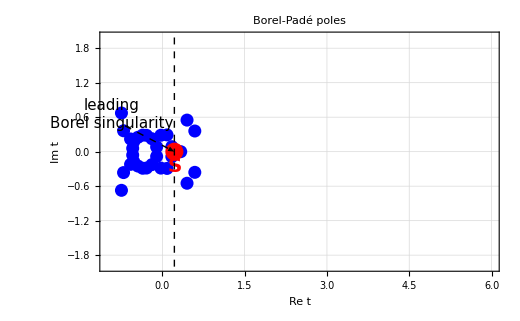

```mathematica
polesPlot=ListPlot[ReIm/@poles,Frame->True,Axes->False,PlotRange->{{-1,6},{-2,2}},PlotStyle->Directive[Blue,PointSize[0.018]],GridLines->Automatic,GridLinesStyle->Directive[GrayLevel[0.85],Dashed],FrameLabel->{Style["Re t",18],Style["Im t",18]},PlotLabel->Style["Borel-Padé poles",20,Bold,Darker[Blue]],ImageSize->520,Epilog->{Red,PointSize[0.025],If[Head[SfromPade]===Missing,{},Point[ReIm[SfromPade]]],Black,If[Head[SfromPade]===Missing,{},{Dashed,Line[{{Re[SfromPade],-2},{Re[SfromPade],2}}],Text[Style["S",20,Bold,Red],{Re[SfromPade],-0.25}],Arrow[{{Re[SfromPade]-0.9,0.45},ReIm[SfromPade]}],Text[Style["leading\nBorel singularity",15,Black],{Re[SfromPade]-1.15,0.65}]}]}];

polesPlot
```

```mathematica
ClearAll[LeadingBorelPoleByRealAxis];

Options[LeadingBorelPoleByRealAxis]={MinRadius->0.15,MaxAngle->Pi/6};

LeadingBorelPoleByRealAxis[poles_List,OptionsPattern[]]:=Module[{rmin,maxang,candidates},rmin=OptionValue[MinRadius];
maxang=OptionValue[MaxAngle];
candidates=Select[poles,Re[N[#]]>0&&Abs[N[#]]>rmin&&Abs[Arg[N[#]]]<maxang&];
If[Length[candidates]==0,Missing["NoPositiveAxisCandidate"],First@SortBy[candidates,Re[N[#]]&]]];
```

```mathematica
SfromPade=LeadingBorelPoleByRealAxis[poles,MinRadius->0.15,MaxAngle->Pi/5];

N[SfromPade,30]
```

0.17301652853414932525824075291-0.086584947757446219924145653335 ⅈ

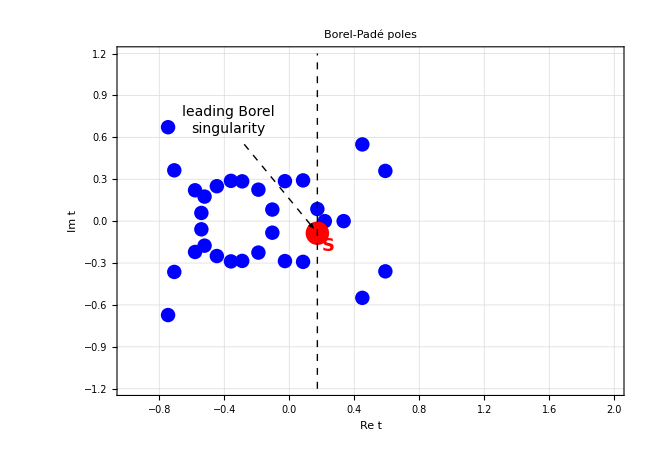

```mathematica
polePts=ReIm/@poles;

xRange={-1,2};
yRange={-1.2,1.2};

polesPlot=ListPlot[polePts,Frame->True,Axes->False,PlotRange->{xRange,yRange},PlotRangePadding->Scaled[0.08],AspectRatio->0.72,PlotStyle->Directive[Blue,PointSize[0.016]],GridLines->Automatic,GridLinesStyle->Directive[GrayLevel[0.86],Dashed],FrameLabel->{Style["Re t",18],Style["Im t",18]},PlotLabel->Style["Borel-Padé poles",22,Bold,Darker[Blue]],ImageSize->650,Epilog->If[Head[SfromPade]===Missing,{},{Red,PointSize[0.026],Point[ReIm[SfromPade]],Black,Dashed,Thick,Line[{{Re[SfromPade],yRange[[1]]},{Re[SfromPade],yRange[[2]]}}],Text[Style["S",18,Bold,Red],{Re[SfromPade]+0.07,-0.18}],Arrowheads[0.035],Arrow[{{Re[SfromPade]-0.45,0.55},ReIm[SfromPade]+{-0.02,0.03}}],Text[Style["leading Borel\nsingularity",14,Black],{Re[SfromPade]-0.55,0.72}]}]];

polesPlot
```

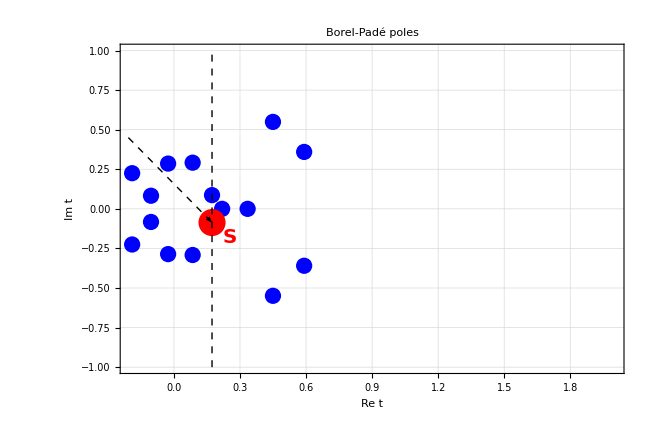

```mathematica
rightPolePts=ReIm/@Select[poles,Re[N[#]]>-0.2&&Abs[Im[N[#]]]<1.2&];

polesPlotClean=ListPlot[rightPolePts,Frame->True,Axes->False,PlotRange->{{-0.2,2.0},{-1.0,1.0}},PlotRangePadding->Scaled[0.08],AspectRatio->0.68,PlotStyle->Directive[Blue,PointSize[0.018]],GridLines->Automatic,GridLinesStyle->Directive[GrayLevel[0.86],Dashed],FrameLabel->{Style["Re t",18],Style["Im t",18]},PlotLabel->Style["Borel-Padé poles",22,Bold,Darker[Blue]],ImageSize->650,Epilog->If[Head[SfromPade]===Missing,{},{Red,PointSize[0.03],Point[ReIm[SfromPade]],Black,Dashed,Thick,Line[{{Re[SfromPade],-1},{Re[SfromPade],1}}],Text[Style["S",20,Bold,Red],{Re[SfromPade]+0.08,-0.18}],Arrowheads[0.035],Arrow[{{Re[SfromPade]-0.38,0.45},ReIm[SfromPade]}],Text[Style["leading Borel\nsingularity",14,Black],{Re[SfromPade]-0.48,0.62}]}]];

polesPlotClean
```

```mathematica
ClearAll[ResurgencePoint];

ResurgencePoint[aVal_?NumericQ,bVal_?NumericQ,lev_Integer,ord_Integer,richOrder_Integer,padeOrder_List,wp_:80]:=Module[{cs,ratios,rich,invSRich,SRich,pade,SPad,invSPad},cs=QuarticCoefficients[aVal,bVal,lev,ord,wp];
ratios=LargeOrderRatioData[cs];
rich=Richardson[ratios,richOrder];
invSRich=Last[rich][[2]];
SRich=1/invSRich;
pade=ActionFromPade[cs,padeOrder,wp];
SPad=pade["S"];
invSPad=If[Head[SPad]===Missing,Missing["NoPole"],1/Re[SPad]];
<|"a"->aVal,"Coefficients"->cs,"InvSFromRichardson"->invSRich,"SFromRichardson"->SRich,"SFromPade"->SPad,"InvSFromPade"->invSPad|>];
```

```mathematica
(* ============================================================*)
(*Large-order ratio*)
(* ============================================================*)

ClearAll[LargeOrderRatioData];

LargeOrderRatioData[coeffs_List]:=Table[{k,coeffs[[k+1]]/(k coeffs[[k]])},{k,1,Length[coeffs]-1}];

(* ============================================================*)
(*Richardson acceleration*)
(* ============================================================*)

ClearAll[Richardson];

Richardson[data_List,pmax_Integer]:=Module[{vals,ks,newVals,newKs,p},vals=data[[All,2]];
ks=data[[All,1]];
For[p=1,p<=pmax&&Length[vals]>=2,p++,newVals=Table[(ks[[j+1]]^p vals[[j+1]]-ks[[j]]^p vals[[j]])/(ks[[j+1]]^p-ks[[j]]^p),{j,1,Length[vals]-1}];
newKs=Most[ks];
vals=newVals;
ks=newKs;];
Transpose[{ks,vals}]];
```

```mathematica
ClearAll[BorelTransformSeries,BorelPade,PadePoles];

BorelTransformSeries[coeffs_List,t_,nmax_:Automatic]:=Module[{n},n=If[nmax===Automatic,Length[coeffs]-1,nmax];
Sum[coeffs[[k+1]]/k! t^k,{k,0,Min[n,Length[coeffs]-1]}]];

BorelPade[coeffs_List,t_,L_Integer,M_Integer]:=Module[{nmax,ser},nmax=Min[Length[coeffs]-1,L+M];
ser=BorelTransformSeries[coeffs,t,nmax];
PadeApproximant[ser,{t,0,{L,M}}]];

PadePoles[rat_,t_,wp_:80]:=Module[{den,roots},den=Denominator[Together[rat]];
roots=t/. NSolve[den==0,t,WorkingPrecision->wp];
N[roots,wp]];

ClearAll[RightHalfPlanePoles,LeadingPadePoleRobust];

RightHalfPlanePoles[poles_List]:=SortBy[Select[poles,Re[N[#]]>0&],{Abs[Arg[N[#]]],Re[N[#]]}&];

LeadingPadePoleRobust[poles_List]:=Module[{right},right=RightHalfPlanePoles[poles];
If[Length[right]==0,Missing["NoRightHalfPlanePole"],First[right]]];

ClearAll[ActionFromPade];

ActionFromPade[coeffs_List,padeOrder_List:{35,35},wp_:80]:=Module[{bp,poles,S},bp=BorelPade[coeffs,t,padeOrder[[1]],padeOrder[[2]]];
poles=PadePoles[bp,t,wp];
S=LeadingPadePoleRobust[poles];
<|"BorelPade"->bp,"PadePoles"->poles,"RightHalfPlanePoles"->RightHalfPlanePoles[poles],"S"->S|>];
```

NSolve::precw: The precision of the argument function ({1.-20. t+200. t^2-2000. t^3+«51»+8.×10^33 t^41+2.×10^33 t^42+3.×10^32 t^43+2.×10^31 t^44+2.×10^29 t^45}) is less than WorkingPrecision (100).

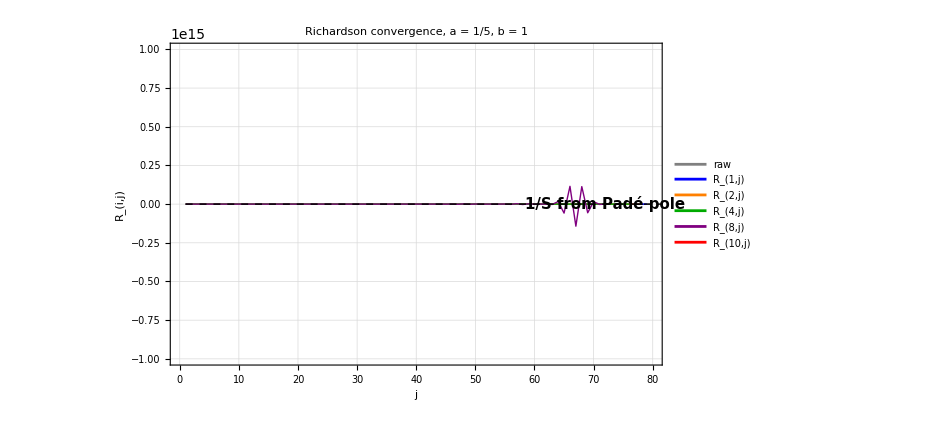

```mathematica
(* ============================================================*)(*Fixed-parameter resurgence test*)(* ============================================================*)a0=1/5;
b0=1;
lev=0;
ord=100;
padeOrder={45,45};

coeffs =N[coeffsSym/. pars,10];

ratioData=LargeOrderRatioData[coeffs];

rich1=Richardson[ratioData,1];
rich2=Richardson[ratioData,2];
rich4=Richardson[ratioData,4];
rich8=Richardson[ratioData,8];
rich10=Richardson[ratioData,10];

padeData=ActionFromPade[coeffs,padeOrder,100];

SfromPade=padeData["S"];
invSfromPade=1/Re[SfromPade];

fig3Analog=ListLinePlot[{ratioData,rich1,rich2,rich4,rich8,rich10},Frame->True,Axes->False,PlotRange->All,PlotStyle->{Directive[Gray,Thin],Directive[Blue,Thick],Directive[Orange,Thick],Directive[Darker[Green],Thick],Directive[Purple,Thick],Directive[Red,Thick]},FrameLabel->{Style["j",18],Style[TraditionalForm[Subscript[R,i,j]],18]},PlotLegends->Placed[{"raw",Subscript["R","1,j"],Subscript["R","2,j"],Subscript["R","4,j"],Subscript["R","8,j"],Subscript["R","10,j"]},{0.78,0.72}],GridLines->Automatic,GridLinesStyle->Directive[GrayLevel[0.85],Dashed],PlotLabel->Style[Row[{"Richardson convergence,  a = ",a0,",  b = ",b0}],20,Bold,Darker[Blue]],ImageSize->700,Epilog->{Black,Dashed,Thick,Line[{{1,invSfromPade},{ord,invSfromPade}}],Text[Style[Row[{"1/S from Padé pole"}],15,Black,Bold],{0.72 ord,1.02 invSfromPade}]}];

fig3Analog
```

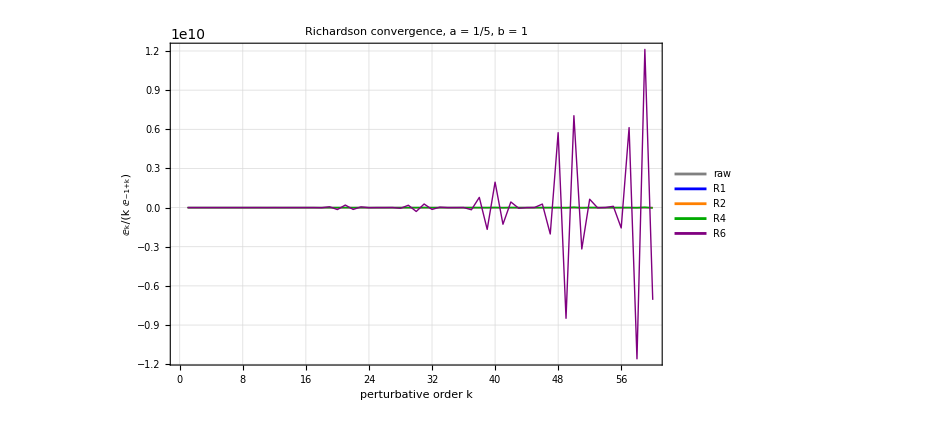

```mathematica
(*Keep only stable Richardson levels*)rich0=ratioData;
rich1=Richardson[ratioData,1];
rich2=Richardson[ratioData,2];
rich4=Richardson[ratioData,4];
rich6=Richardson[ratioData,6];

(*Trim the unstable tail*)
trim[data_,kmax_]:=Select[data,#[[1]]<=kmax&];

kmaxPlot=60;

stableData=trim[#,kmaxPlot]&/@{rich0,rich1,rich2,rich4,rich6};

figStable=ListLinePlot[stableData,Frame->True,Axes->False,PlotRange->All,PlotStyle->{Directive[Gray,Thin],Directive[Blue,Thick],Directive[Orange,Thick],Directive[Darker[Green],Thick],Directive[Purple,Thick]},GridLines->Automatic,GridLinesStyle->Directive[GrayLevel[0.85],Dashed],FrameLabel->{Style["perturbative order k",18],Style[TraditionalForm[Subscript[E,k]/(k Subscript[E,k-1])],18]},PlotLegends->Placed[{"raw","R1","R2","R4","R6"},{0.78,0.75}],PlotLabel->Style[Row[{"Richardson convergence,  a = ",a0,",  b = ",b0}],20,Bold,Darker[Blue]],ImageSize->700];

figStable
```

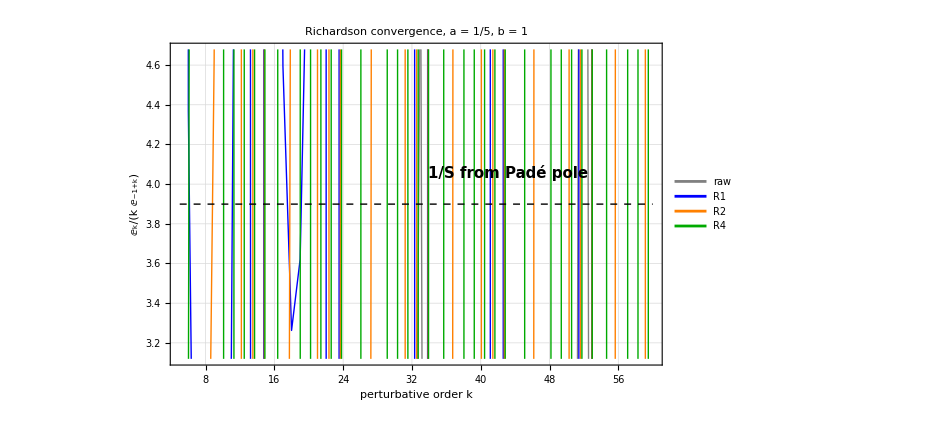

```mathematica
kmaxPlot=60;

stableData=(Select[#,5<=#[[1]]<=kmaxPlot&]&)/@{ratioData,rich1,rich2,rich4};

invS=invSfromPade;

figStableZoom=ListLinePlot[stableData,Frame->True,Axes->False,PlotRange->{{5,kmaxPlot},{0.8 invS,1.2 invS}},PlotStyle->{Directive[Gray,Thin],Directive[Blue,Thick],Directive[Orange,Thick],Directive[Darker[Green],Thick]},GridLines->Automatic,GridLinesStyle->Directive[GrayLevel[0.85],Dashed],FrameLabel->{Style["perturbative order k",18],Style[TraditionalForm[Subscript[E,k]/(k Subscript[E,k-1])],18]},PlotLegends->Placed[{"raw","R1","R2","R4"},{0.80,0.75}],Epilog->{Black,Dashed,Thick,Line[{{5,invS},{kmaxPlot,invS}}],Text[Style["1/S from Padé pole",15,Black,Bold],{0.72 kmaxPlot,1.04 invS}]},PlotLabel->Style[Row[{"Richardson convergence,  a = ",a0,",  b = ",b0}],20,Bold,Darker[Blue]],ImageSize->700];

figStableZoom
```

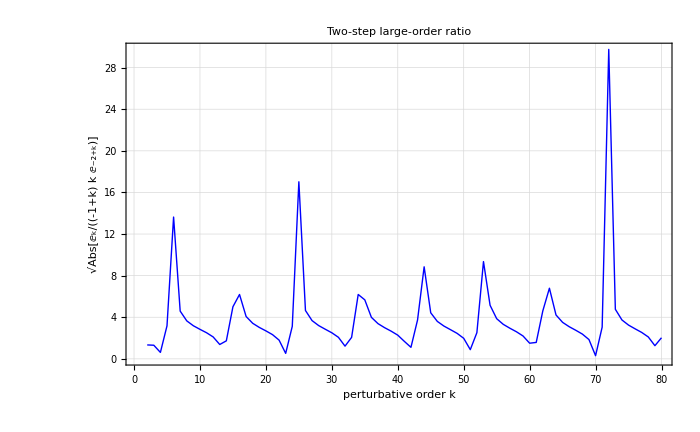

```mathematica
ClearAll[TwoStepRatioData];

TwoStepRatioData[cs_List]:=Table[If[cs[[k-1]]=!=0,{k,Sqrt[Abs[cs[[k+1]]/(k (k-1) cs[[k-1]])]]},Nothing],{k,2,Length[cs]-1}];

twoStepData=TwoStepRatioData[coeffs];

twoStepPlot=ListLinePlot[twoStepData,Frame->True,Axes->False,PlotRange->All,PlotStyle->Directive[Blue,Thick],GridLines->Automatic,GridLinesStyle->Directive[GrayLevel[0.85],Dashed],FrameLabel->{Style["perturbative order k",18],Style[TraditionalForm[Sqrt[Abs[Subscript[E,k]/(k (k-1) Subscript[E,k-2])]]],18]},PlotLabel->Style["Two-step large-order ratio",20,Bold,Darker[Blue]],ImageSize->700];

twoStepPlot
```

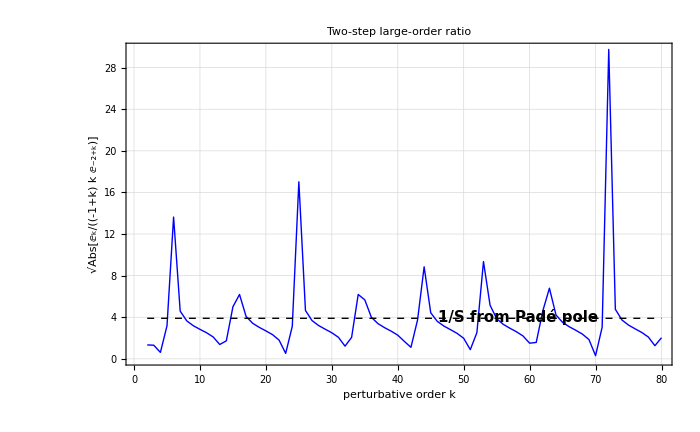

```mathematica
invS=1/Re[SfromPade];

twoStepPlotWithS=Show[twoStepPlot,Graphics[{Black,Dashed,Thick,Line[{{2,invS},{Length[coeffs]-1,invS}}],Text[Style["1/S from Padé pole",15,Black,Bold],{0.72 Length[coeffs],1.03 invS}]}]];

twoStepPlotWithS
```

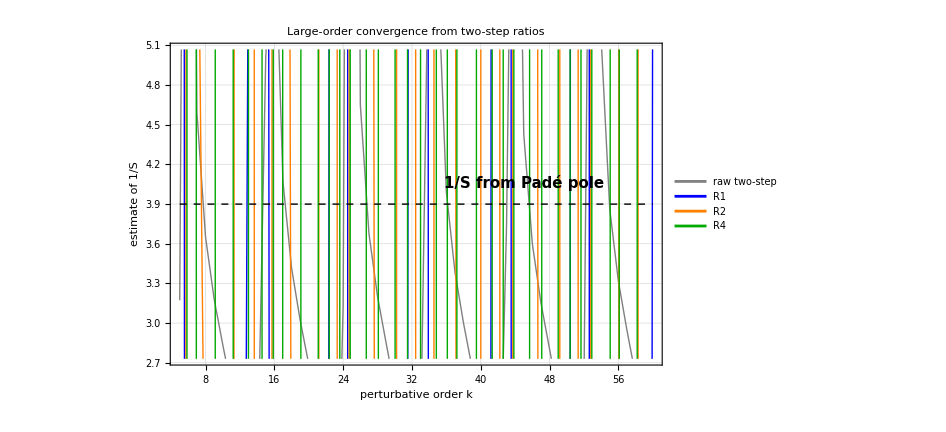

```mathematica
rich1Two=Richardson[twoStepData,1];
rich2Two=Richardson[twoStepData,2];
rich4Two=Richardson[twoStepData,4];

stableTwoStep=(Select[#,5<=#[[1]]<=60&]&)/@{twoStepData,rich1Two,rich2Two,rich4Two};

twoStepRichPlot=ListLinePlot[stableTwoStep,Frame->True,Axes->False,PlotRange->{{5,60},{0.7 invS,1.3 invS}},PlotStyle->{Directive[Gray,Thin],Directive[Blue,Thick],Directive[Orange,Thick],Directive[Darker[Green],Thick]},GridLines->Automatic,GridLinesStyle->Directive[GrayLevel[0.85],Dashed],FrameLabel->{Style["perturbative order k",18],Style["estimate of 1/S",18]},PlotLegends->Placed[{"raw two-step","R1","R2","R4"},{0.78,0.75}],Epilog->{Black,Dashed,Thick,Line[{{5,invS},{60,invS}}],Text[Style["1/S from Padé pole",15,Black,Bold],{45,1.04 invS}]},PlotLabel->Style["Large-order convergence from two-step ratios",20,Bold,Darker[Blue]],ImageSize->700];

twoStepRichPlot
```

```mathematica
smallCoeffTable=Select[Table[{k,coeffs[[k+1]],Abs[coeffs[[k+1]]]},{k,0,Length[coeffs]-1}],#[[3]]<10^-30&];

smallCoeffTable
```

{}

```mathematica
(* ============================================================*)(*Resurgence closure plot*)(* ============================================================*)ClearAll[LargeOrderPrediction];

LargeOrderPrediction[k_Integer,S_,beta_,C_,instCoeffs_List,M_Integer]:=Module[{mmax},mmax=Min[M,Length[instCoeffs]-1];
C Sum[instCoeffs[[n+1]] Gamma[k+beta-n]/S^(k+beta-n),{n,0,mmax}]];
```

```mathematica
ClearAll[EstimateStokesPrefactor];

EstimateStokesPrefactor[pertCoeffs_List,S_,beta_,inst0_:1,kmin_:40,kmax_:Automatic]:=Module[{kmaxUse,vals},kmaxUse=If[kmax===Automatic,Length[pertCoeffs]-1,kmax];
vals=Table[pertCoeffs[[k+1]] S^(k+beta)/(inst0 Gamma[k+beta]),{k,kmin,kmaxUse}];
Median[vals]];
```

```mathematica
S=Re[SfromPade];
beta=0;  (*first try;adjust later if you know the one-loop exponent*)

Cest=EstimateStokesPrefactor[coeffs,S,beta,1,40,70];

N[Cest,30]
```

-2.224429055×10^-8

```mathematica
instCoeffs={1};
```

```mathematica
ClearAll[ResurgenceClosureData];

ResurgenceClosureData[pertCoeffs_List,S_,beta_,C_,instCoeffs_List,M_Integer,kmin_Integer,kmax_Integer]:=Table[With[{actual=pertCoeffs[[k+1]],pred=LargeOrderPrediction[k,S,beta,C,instCoeffs,M]},{k,Log10[Abs[(actual-pred)/actual]]}],{k,kmin,kmax}];
```

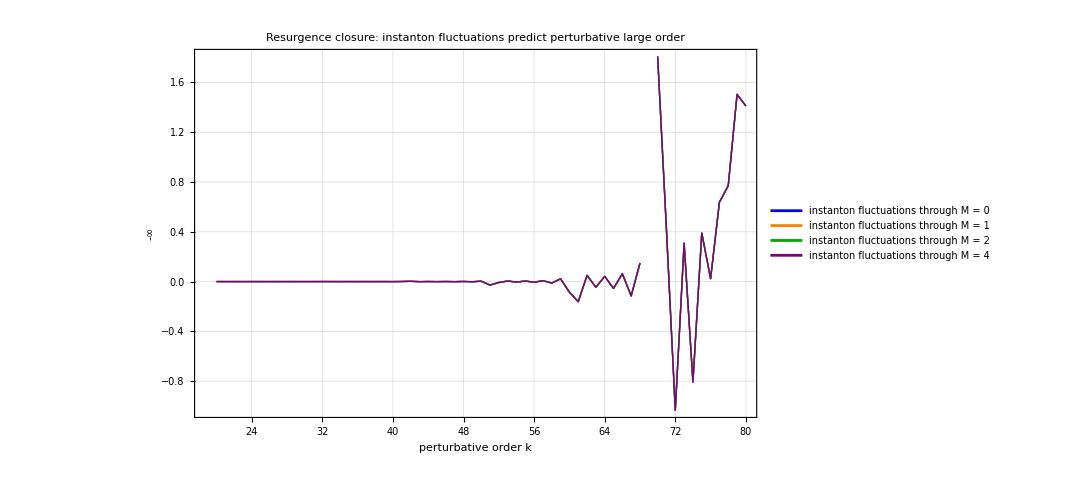

```mathematica
kmin=20;
kmax=Min[Length[coeffs]-1,80];

(*Replace these when you compute direct one-instanton fluctuations*)
instCoeffs={1,0,0,0,0};

Ms={0,1,2,4};

closureCurves=Table[ResurgenceClosureData[coeffs,S,beta,Cest,instCoeffs,M,kmin,kmax],{M,Ms}];

closurePlot=ListLinePlot[closureCurves,Frame->True,Axes->False,PlotRange->All,PlotStyle->{Directive[Blue,Thick],Directive[Orange,Thick],Directive[Darker[Green],Thick],Directive[Purple,Thick]},GridLines->Automatic,GridLinesStyle->Directive[GrayLevel[0.85],Dashed],FrameLabel->{Style["perturbative order k",18],Style[TraditionalForm[Log10[Abs[(Subscript[E,k]^(0)-Subscript[E,k,pred]^(0))/Subscript[E,k]^(0)]]],18]},PlotLegends->Placed[Table[Row[{"instanton fluctuations through M = ",M}],{M,Ms}],{0.55,0.78}],PlotLabel->Style["Resurgence closure: instanton fluctuations predict perturbative large order",20,Bold,Darker[Blue]],ImageSize->800];

closurePlot
```

```mathematica
ClearAll[ExtractInstantonFluctuations];

ExtractInstantonFluctuations[pertCoeffs_List,S_,beta_,C_,nmax_Integer,kmin_Integer,kmax_Integer]:=Module[{x,data,basis,fit,pars},data=Table[{k,pertCoeffs[[k+1]]/(C Gamma[k+beta]/S^(k+beta))},{k,kmin,kmax}];
basis=Table[S^n Gamma[x+beta-n]/Gamma[x+beta],{n,0,nmax}];
fit=LinearModelFit[data,basis,x];
pars=fit["BestFitParameters"];
pars];
```

```mathematica
nmax=4;

extractedInstCoeffs=ExtractInstantonFluctuations[coeffs,S,beta,Cest,nmax,35,75];

N[extractedInstCoeffs,30]
```

{-231883.974,1.83244919×10^8,-5.20874964×10^10,6.29983215×10^12,-2.73109355×10^14}

```mathematica
directInstCoeffs=Take[instCoeffs,nmax+1];

comparisonData=Table[{n,directInstCoeffs[[n+1]],extractedInstCoeffs[[n+1]],extractedInstCoeffs[[n+1]]/directInstCoeffs[[n+1]]},{n,0,nmax}];

comparisonData//TableForm
```

Power::infy: Infinite expression 1/0 encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

0 | 1 | -231883.974 | -231883.974
1 | 0 | 1.83244919×10^8 | ComplexInfinity
2 | 0 | -5.20874964×10^10 | ComplexInfinity
3 | 0 | 6.29983215×10^12 | ComplexInfinity
4 | 0 | -2.73109355×10^14 | ComplexInfinity

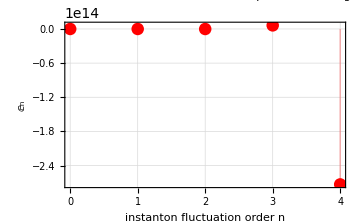

```mathematica
instExtractionPlot=ListPlot[Table[{n,extractedInstCoeffs[[n+1]]},{n,0,nmax}],Frame->True,Axes->False,PlotStyle->Directive[Red,PointSize[0.025]],Filling->Axis,GridLines->Automatic,GridLinesStyle->Directive[GrayLevel[0.85],Dashed],FrameLabel->{Style["instanton fluctuation order n",15],Style[TraditionalForm[Subscript[E,n]^(1)],15]},PlotLabel->Style["Instanton fluctuations reconstructed from perturbative large order",15,Bold,Darker[Blue]],ImageSize->360];

instExtractionPlot
```

```mathematica
ClearAll[LargeOrderBasisTerm];

LargeOrderBasisTerm[k_,S_,beta_,n_]:=Gamma[k+beta-n]/S^(k+beta-n);
```

```mathematica
ClearAll[FitLargeOrderTower];

FitLargeOrderTower[coeffs_List,S_,beta_,M_Integer,kfitmin_Integer,kfitmax_Integer]:=Module[{data,pars,model,fit,k},data=Table[{kk,coeffs[[kk+1]]},{kk,kfitmin,kfitmax}];
pars=Array[A,M+1,0];
model=Sum[pars[[n+1]] LargeOrderBasisTerm[k,S,beta,n],{n,0,M}];
fit=LinearModelFit[data,model,pars,k];
<|"Fit"->fit,"Parameters"->fit["BestFitParameters"],"Model"->model|>];
```

```mathematica
ClearAll[LargeOrderReconstructionError];

LargeOrderReconstructionError[coeffs_List,S_,beta_,M_Integer,kfitmin_Integer,kfitmax_Integer,kplotmin_Integer,kplotmax_Integer]:=Module[{fitObj,pars,pred},fitObj=FitLargeOrderTower[coeffs,S,beta,M,kfitmin,kfitmax];
pars=fitObj["Parameters"];
Table[pred=Sum[pars[[n+1]] LargeOrderBasisTerm[kk,S,beta,n],{n,0,M}];
{kk,Log10[Abs[(coeffs[[kk+1]]-pred)/coeffs[[kk+1]]]]},{kk,kplotmin,kplotmax}]];
```

```mathematica
Ms={0,1,2,3,4};

kfitmin=30;
kfitmax=65;

kplotmin=20;
kplotmax=80;

closureCurves=Table[LargeOrderReconstructionError[coeffs,S,beta,M,kfitmin,kfitmax,kplotmin,kplotmax],{M,Ms}];

bangClosurePlot=ListLinePlot[closureCurves,Frame->True,Axes->False,PlotRange->{{kplotmin,kplotmax},All},PlotStyle->{Directive[Blue,Thick],Directive[Orange,Thick],Directive[Darker[Green],Thick],Directive[Purple,Thick],Directive[Red,Thick]},GridLines->Automatic,GridLinesStyle->Directive[GrayLevel[0.85],Dashed],FrameLabel->{Style["perturbative order k",18],Style[TraditionalForm[Log10[Abs[(Subscript[E,k]^(0)-Subscript[E,k,pred]^(0))/Subscript[E,k]^(0)]]],18]},PlotLegends->Placed[Table[Row[{"large-order ansatz through M = ",M}],{M,Ms}],{0.58,0.75}],PlotLabel->Style["Resurgence closure: instanton tower reconstructed from perturbative large order",20,Bold,Darker[Blue]],ImageSize->850];

bangClosurePlot
```

LinearModelFit::nonopt: Options expected (instead of k$514685) beyond position 3 in LinearModelFit[{{30,3.452998857×10^45},{31,-1.966556039×10^47},{32,5.113048455×10^48},{33,8.855100036×10^50},«28»,{62,4.028128967×10^113},{63,-1.200986477×10^116},{64,2.890859356×10^118},{65,-6.150026634×10^120}},(«122»)^-k$514685 A[0] Gamma[k$514685],{«1»},k$514685]. An option must be a rule or a list of rules.

LinearModelFit::nonopt: Options expected (instead of k$514696) beyond position 3 in LinearModelFit[{{30,3.452998857×10^45},{31,-1.966556039×10^47},{32,5.113048455×10^48},{33,8.855100036×10^50},«28»,{62,4.028128967×10^113},{63,-1.200986477×10^116},{64,2.890859356×10^118},{65,-6.150026634×10^120}},(«122»)^(1-k$514696) A[1] Gamma[-1+«8»]+«1»,«1»,k$514696]. An option must be a rule or a list of rules.

Part::partw: Part 2 of «1»[BestFitParameters] does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

LinearModelFit::nonopt: Options expected (instead of k$514715) beyond position 3 in LinearModelFit[{{30,3.452998857×10^45},{31,-1.966556039×10^47},{32,5.113048455×10^48},{33,8.855100036×10^50},«28»,{62,4.028128967×10^113},{63,-1.200986477×10^116},{64,2.890859356×10^118},{65,-6.150026634×10^120}},«1»,{A[0],A[1],A[2]},k$514715]. An option must be a rule or a list of rules.

General::stop: Further output of LinearModelFit::nonopt will be suppressed during this calculation.

LinearModelFit::nonopt: Options expected (instead of k$514696) beyond position 3 in LinearModelFit[{{30.,3.452998857×10^45},{31.,-1.966556039×10^47},{32.,5.113048455×10^48},{33.,8.855100036×10^50},«28»,{62.,4.028128967×10^113},{63.,-1.200986477×10^116},{64.,2.890859356×10^118},{65.,-6.150026634×10^120}},«2»,k$514696]. An option must be a rule or a list of rules.

Part::partw: Part 2 of LinearModelFit[{{30.,3.452998857×10^45},{31.,-1.966556039×10^47},{32.,5.113048455×10^48},{33.,8.855100036×10^50},«28»,{62.,4.028128967×10^113},{63.,-1.200986477×10^116},{64.,2.890859356×10^118},{65.,-6.150026634×10^120}},«2»,«8»][…] does not exist.

LinearModelFit::nonopt: Options expected (instead of k$514715) beyond position 3 in LinearModelFit[{{30.,3.452998857×10^45},{31.,-1.966556039×10^47},{32.,5.113048455×10^48},{33.,8.855100036×10^50},«28»,{62.,4.028128967×10^113},{63.,-1.200986477×10^116},{64.,2.890859356×10^118},{65.,-6.150026634×10^120}},«2»,k$514715]. An option must be a rule or a list of rules.

Part::partw: Part 2 of LinearModelFit[{{30.,3.452998857×10^45},{31.,-1.966556039×10^47},{32.,5.113048455×10^48},{33.,8.855100036×10^50},«28»,{62.,4.028128967×10^113},{63.,-1.200986477×10^116},{64.,2.890859356×10^118},{65.,-6.150026634×10^120}},«2»,«8»][…] does not exist.

Part::partw: Part 3 of LinearModelFit[{{30.,3.452998857×10^45},{31.,-1.966556039×10^47},{32.,5.113048455×10^48},{33.,8.855100036×10^50},«28»,{62.,4.028128967×10^113},{63.,-1.200986477×10^116},{64.,2.890859356×10^118},{65.,-6.150026634×10^120}},«2»,«8»][…] does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

LinearModelFit::nonopt: Options expected (instead of k$514728) beyond position 3 in LinearModelFit[{{30.,3.452998857×10^45},{31.,-1.966556039×10^47},{32.,5.113048455×10^48},{33.,8.855100036×10^50},«28»,{62.,4.028128967×10^113},{63.,-1.200986477×10^116},{64.,2.890859356×10^118},{65.,-6.150026634×10^120}},«2»,k$514728]. An option must be a rule or a list of rules.

General::stop: Further output of LinearModelFit::nonopt will be suppressed during this calculation.

-Graphics-

## Richardson Accel

```mathematica
ClearAll[PadePoles];

PadePoles[rat_,t_,wp_:80]:=Module[{den,roots},den=Denominator[Together[rat]];
roots=t/. NSolve[den==0,t,WorkingPrecision->wp];
N[roots,wp]];

ClearAll[RightHalfPlanePoles];

RightHalfPlanePoles[poles_List]:=SortBy[Select[poles,Re[N[#]]>0&],{Abs[Arg[N[#]]],Re[N[#]]}&];

ClearAll[LeadingPadePoleRobust];

LeadingPadePoleRobust[poles_List]:=Module[{right},right=RightHalfPlanePoles[poles];
If[Length[right]==0,Missing["NoRightHalfPlanePole"],First[right]]];
```

```mathematica
ClearAll[LeadingBorelPole];

Options[LeadingBorelPole]={ImaginaryTolerance->10^-2};

LeadingBorelPole[poles_List,OptionsPattern[]]:=Module[{tol,candidates},tol=OptionValue[ImaginaryTolerance];
candidates=Select[poles,Re[#]>0&&Abs[Im[#]]<tol Max[1,Abs[Re[#]]]&];
If[Length[candidates]==0,Missing["None"],First[SortBy[candidates,Re]]]];
```

```mathematica
ClearAll[Richardson];

Richardson[data_List,pmax_Integer]:=Module[{vals,ks,newVals,newKs,p},vals=data[[All,2]];
ks=data[[All,1]];
For[p=1,p<=pmax&&Length[vals]>=2,p++,newVals=Table[(ks[[j+1]]^p vals[[j+1]]-ks[[j]]^p vals[[j]])/(ks[[j+1]]^p-ks[[j]]^p),{j,1,Length[vals]-1}];
newKs=Most[ks];
vals=newVals;
ks=newKs;];
Transpose[{ks,vals}]];
```

```mathematica
ClearAll[BorelPadeSum];

Options[BorelPadeSum]={WorkingPrecision->80,AccuracyGoal->40,PrecisionGoal->40,MaxRecursion->40,DirectionAngle->0};

BorelPadeSum[coeffs_List,z0_?NumericQ,L_Integer,M_Integer,OptionsPattern[]]:=Module[{t,s,theta,bpExpr,wp,ag,pg,mr,z},theta=OptionValue[DirectionAngle];
wp=OptionValue[WorkingPrecision];
ag=OptionValue[AccuracyGoal];
pg=OptionValue[PrecisionGoal];
mr=OptionValue[MaxRecursion];
z=SetPrecision[z0,wp];
bpExpr=BorelPade[coeffs,t,L,M];
NIntegrate[Evaluate[Exp[-s]*(bpExpr/. t->z s Exp[I theta])*Exp[I theta]],{s,0,Infinity},WorkingPrecision->wp,AccuracyGoal->ag,PrecisionGoal->pg,MaxRecursion->mr,Method->{"GlobalAdaptive","SymbolicProcessing"->0}]];
```

## analyses

```mathematica
ClearAll[AnalyzeAsymmetricQuartic];

Options[AnalyzeAsymmetricQuartic]={Order->80,Level->0,Parameters->{a->1/5,b->1},PadeOrder->{35,35},ZValue->0.05,WorkingPrecision->80};

AnalyzeAsymmetricQuartic[OptionsPattern[]]:=Module[{ord,lev,pars,pade,z0,wp,raw,cs,t,bp,poles,realPoles,ratioData,leadingPole,richOrder, rich4,invS,Sratio,sum},
ord=OptionValue[Order];
lev=OptionValue[Level];
pars=OptionValue[Parameters];
pade=OptionValue[PadeOrder];
z0=OptionValue[ZValue];
wp=OptionValue[WorkingPrecision];

If[Total[pade]>ord,Print["Warning: PadeOrder too high for available coefficients. Reducing it."];
pade={Floor[ord/2],Floor[ord/2]};];

raw=BenderWu[x^2/2+a x^3+b x^4,x,lev,ord,Simplify->True];
cs=N[BWProcess[raw,Output->"Energy",OutputStyle->"Array"]/. pars,wp];

bp=BorelPade[cs,t,pade[[1]],pade[[2]]];

poles=PadePoles[bp,t,wp];

rightHalfPoles=RightHalfPlanePoles[poles];

leadingPole=LeadingPadePoleRobust[poles];

ratioData=Table[{k,cs[[k+1]]/(k cs[[k]])},{k,1,Length[cs]-1}];

richOrder=Min[4,Length[ratioData]-2];

rich4=Richardson[ratioData,richOrder];

invS=If[ListQ[rich4]&&Length[rich4]>0&&Length[Last[rich4]]>=2,Last[rich4][[2]],Missing["NotEnoughData"]];

Sratio=If[NumberQ[invS],1/invS,Missing["NotEnoughData"]];

sum=BorelPadeSum[cs,z0,pade[[1]],pade[[2]],WorkingPrecision->wp];

<|"Coefficients"->cs,
"BorelPade"->bp,
"PadePoles"->poles,
"RightHalfPlanePoles"->rightHalfPoles,
"LeadingPadePole"->leadingPole,
"RatioData"->ratioData,
"Richardson4"->rich4,
"SFromRatios"->Sratio,
"BorelPadeSum"->sum|>
];
```

```mathematica
res=AnalyzeAsymmetricQuartic[Order->10,Level->0,Parameters->{a->1/5,b->1},PadeOrder->{4,4},ZValue->0.05];

res["LeadingPadePole"]
res["SFromRatios"]
res["BorelPadeSum"]
```

NSolve::precw: The precision of the argument function ({-0.25497331444598390382916234678061767589422684836932151118851243750868277276503-«116» t$468453-«116» t$468453^2+«116» t$468453^3+1. t$468453^4}) is less than WorkingPrecision (80).

NIntegrate::precw: The precision of the argument function ((ⅇ^-s$468592 (0.5+«116» s$468592+«116» s$468592^2-«115» s$468592^3-«116» s$468592^4))/(1+«6»)) is less than WorkingPrecision (80.).

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 60 recursive bisections in s$468592 near {s$468592} = {17.823740183663221969387986026349248910707398902774200992765485983431721749374824}. NIntegrate obtained 0.53105904646671104935005116376054325138621729903344120659192652607421126055077041 and 1.8981977305997927159829650502146945852798727534235279941262392531904915699212368×10^-9 for the integral and error estimates.

0.89118700918316114980116775406329169746268151899214379498387709980360864031985122

0.3599587445204926263980976113292275121366676156673306644967248951099392908165

0.53105904646671104935005116376054325138621729903344120659192652607421126055077041

```mathematica
res=AnalyzeAsymmetricQuartic[Order->10,Level->0,Parameters->{a->1/5,b->1},PadeOrder->{4,4},ZValue->0.05];

N[res["PadePoles"],30]
N[res["RightHalfPlanePoles"],30]
N[res["LeadingPadePole"],30]
```

NSolve::precw: The precision of the argument function ({-0.25497331444598390382916234678061767589422684836932151118851243750868277276503-«116» t$468992-«116» t$468992^2+«116» t$468992^3+1. t$468992^4}) is less than WorkingPrecision (80).

NIntegrate::precw: The precision of the argument function ((ⅇ^-s$469140 (0.5+«116» s$469140+«116» s$469140^2-«115» s$469140^3-«116» s$469140^4))/(1+«6»)) is less than WorkingPrecision (80.).

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 60 recursive bisections in s$469140 near {s$469140} = {17.823740183663221969387986026349248910707398902774200992765485983431721749374824}. NIntegrate obtained 0.53105904646671104935005116376054325138621729903344120659192652607421126055077041 and 1.8981977305997927159829650502146945852798727534235279941262392531904915699212368×10^-9 for the integral and error estimates.

{-2.51139526395318623311602296465,-0.318770467151380937341967967932-0.11094246917104242760183358544 ⅈ,-0.318770467151380937341967967932+0.11094246917104242760183358544 ⅈ,0.891187009183161149801167754063}

{0.891187009183161149801167754063}

0.891187009183161149801167754063

```mathematica
res=AnalyzeAsymmetricQuartic[Order->80,Level->0,Parameters->{a->1/5,b->1},PadeOrder->{35,35},ZValue->0.05,WorkingPrecision->80];
```

NSolve::precw: The precision of the argument function ({0.0057419248568739646662601197294451010751346625030345961574022+0.325462339491523008688313725709091579438719767862140635979671 t$483972+«33»+1. t$483972^35}) is less than WorkingPrecision (80).

NIntegrate::precw: The precision of the argument function ((ⅇ^-s$484741 (0.5+«116» s$484741+«115» s$484741^2+«116» «1»+«29»+«103» («8»)^33+«99» s$484741^34+«96» s$484741^35))/(1+«34»+5.06865401101374769501290196029406732022146293394105461917825045056438064082609×10^-44 «1»)) is less than WorkingPrecision (80.).

```mathematica
ClearAll[NearPositiveRealPoles];

NearPositiveRealPoles[poles_List,tol_:10^-4]:=SortBy[Select[poles,Re[#]>0&&Abs[Im[#]]<tol Max[1,Abs[Re[#]]]&],Re];

bp=BorelPade[coeffs,t,4,4];

poles=t/. NSolve[Denominator[Together[bp]]==0,t,WorkingPrecision->80];

N[poles,30]

nearRealPoles=NearPositiveRealPoles[poles,10^-2];

N[nearRealPoles,30]
```

NSolve::precw: The precision of the argument function ({-0.254973314-1.24231619 t-1.09125091 t^2+2.25774919 t^3+1. t^4}) is less than WorkingPrecision (80).

{-2.51139526455461610690657307025,-0.318770467089308653515339207861-0.11094246927241061264072331255 ⅈ,-0.318770467089308653515339207861+0.11094246927241061264072331255 ⅈ,0.891187009106004888815695570245}

{0.891187009106004888815695570245}

```mathematica
SfromPole=If[Length[nearRealPoles]>0,First[nearRealPoles],Missing["NoNearRealPole"]]
```

0.89118700910600488881569557024547656652025262344944626089713846582006682369010565

```mathematica
sPoleApprox=17.8237401835715;
z0=0.05;

SPoleApprox=z0 sPoleApprox
```

0.891187

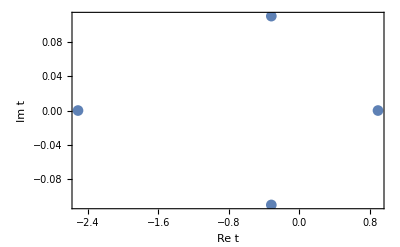

```mathematica
ListPlot[ReIm/@poles,Frame->True,Axes->False,FrameLabel->{"Re t","Im t"},PlotRange->All,PlotMarkers->Automatic]
```

```mathematica
rightHalfPoles=SortBy[Select[poles,Re[#]>0&],Re];

N[rightHalfPoles,30]
```

{0.891187009106004888815695570245}

### periods

```mathematica
V[x_]:=x^2/2+a x^3+b x^4;

(*Solve for classical turning points:V(x)=E*)
tp=x/. NSolve[V[x]==Ε,x];

(*For numerical tests,pick some E and parameters*)
params={a->1/5,b->1};
E0=0.5;
tpNum=tp/. params/. Ε->E0//N
```

{-0.0664015-0.994813 ⅈ,-0.0664015+0.994813 ⅈ,-0.743609,0.676412}

```mathematica
(*Classical A-period:integrate between the two inner turning points*)Aperiod=NIntegrate[Sqrt[2*(E0-V[x])]/. params,{x,tpNum[[3]],tpNum[[4]]}]

(*Classical B-period:between the outer turning points/tunneling cycle*)
Bperiod=NIntegrate[Sqrt[2*(E0-V[x])]/. params,{x,tpNum[[1]],tpNum[[2]]}]
```

1.18158

-1.2078×10^-15+1.88133 ⅈ